```mathematica
density=0.02;
```

```mathematica
(*upper and lower shocks*)
su[x_]:=If[x<U*H/(2q),0.5U*H-(x)*q*(1-ϕ0),0.5U*H*ϕ0]
sl[x_]:=If[x<U*H/(2q),(x)*q*ϕ0,0.5U*H*ϕ0]
(*characteristic curves*)
ψ[x_,ψ0_]:=If[x<(U*H/2-ψ0)/(q*ϕ0) && x<ψ0/(q*(1-ϕ0)),ψ0-q*x(1-2*ϕ0)]
```

```mathematica
H=U=q=1;
ϕ0=0.7;
```

```mathematica
l=Table[ψ[x,ψ0],{ψ0,0,0.5,0.01}];
```

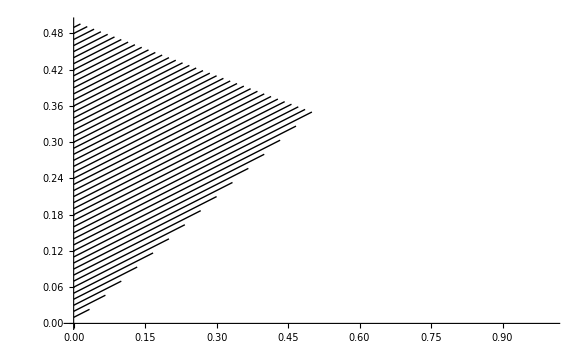

```mathematica
p1=Plot[l,{x,0,1},PlotStyle->{Black}]
```

```mathematica
SetOptions[Plot,PlotStyle->Thick];
```

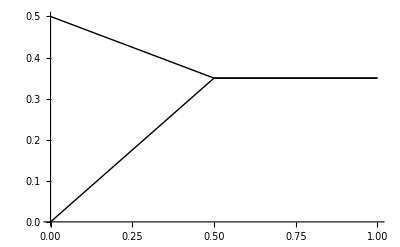

```mathematica
p2=Plot[{su[x],sl[x]},{x,0,1},PlotStyle->{Black}]
```

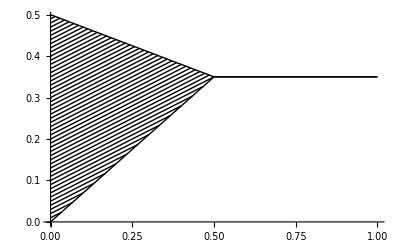

```mathematica
Show[p1,p2]
```

```mathematica
ψ1[x_,ψ0_]:=ψ0-q*x(1-2*ϕ0)
```

```mathematica
l1=Table[ψ1[x,ψ0],{ψ0,0,0.5,density}];
```

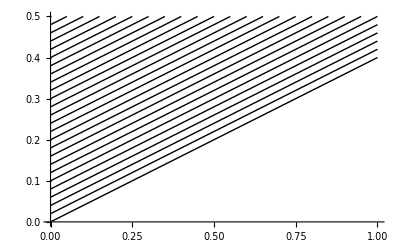

```mathematica
Plot[l1,{x,0,1},PlotStyle->{Black},PlotRange->{{0,1},{0,0.5}}]
```

```mathematica
ψ2[x_,ψ0_]:=If[x<ψ0/(q*(1-ϕ0)),ψ0-q*x(1-2*ϕ0)]
```

```mathematica
l2=Table[ψ2[x,ψ0],{ψ0,0,0.5,density}];
```

```mathematica
sl1[x_]:=(x)*q*ϕ0
```

```mathematica
ψs2[x_,ψ0_,x0_]:=If[x>x0,ψ0-q*(x-x0)]
```

```mathematica
smalls2=Table[ψs2[x,ψ0,ψ0/(q*ϕ0)],{ψ0,0,0.5,density*ϕ0}];
```

```mathematica
p2smalls=Plot[smalls2,{x,0,1},PlotStyle->{Black},PlotRange->{{0,1},{0,0.5}}];
```

```mathematica
jumpStyle=Thickness[0.01];
```

```mathematica
p2a=Plot[sl1[x],{x,0,1},PlotStyle->jumpStyle];
```

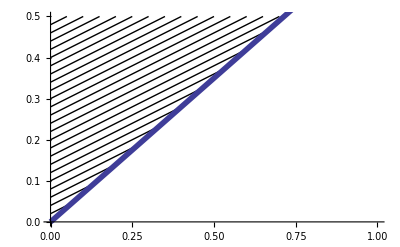

```mathematica
Show[Plot[l2,{x,0,1},PlotStyle->{Black},PlotRange->{{0,1},{0,0.5}}],p2a]
```

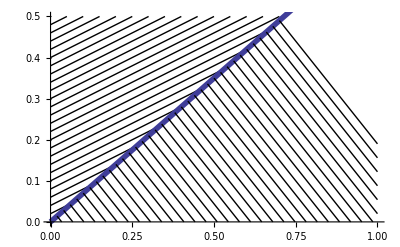

```mathematica
Show[Plot[l2,{x,0,1},PlotStyle->{Black},PlotRange->{{0,1},{0,0.5}}],p2a,p2smalls]
```

```mathematica
p3a=Plot[sl[x],{x,0,1},PlotStyle->jumpStyle];
```

```mathematica
ψ3[x_,ψ0_]:=If[x<ψ0/(q*(1-ϕ0))||ψ0>(1-ϕ0)/2,ψ0-q*x(1-2*ϕ0)]
```

```mathematica
l3=Table[ψ3[x,ψ0],{ψ0,0,0.5,density}];
```

```mathematica
ψs3[x_,ψ0_,x0_]:=If[x>x0&&x>(ψ0-ϕ0/2)/q+x0,ψ0-q*(x-x0)]
```

```mathematica
smalls3=Table[ψs3[x,ψ0,ψ0/(q*ϕ0)],{ψ0,0,1,density*ϕ0}];
```

```mathematica
p3smalls=Plot[smalls3,{x,0,1},PlotStyle->{Black},PlotRange->{{0,1},{0,0.5}}];
```

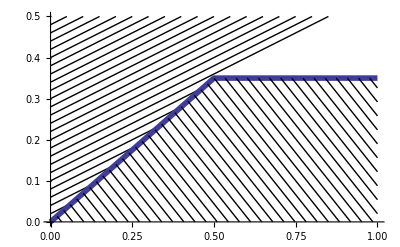

```mathematica
Show[Plot[l3,{x,0,1},PlotStyle->{Black},PlotRange->{{0,1},{0,0.5}}],p3a,p3smalls]
```

```mathematica
su4[x_]:=If[x<U*H/(2q),0.5U*H-(x)*q*(1-ϕ0),0.5U*H*ϕ0]
```

```mathematica
p4b=Plot[su4[x],{x,0,1},PlotStyle->jumpStyle];
```

```mathematica
p4a=p3a;
```

```mathematica
ψ4[x_,ψ0_]:=If[x<(U*H/2-ψ0)/(q*ϕ0) && x<ψ0/(q*(1-ϕ0)),ψ0-q*x(1-2*ϕ0)]
```

```mathematica
l4=Table[ψ4[x,ψ0],{ψ0,0,0.5,density}];
```

```mathematica
p4smalls=p3smalls;
```

```mathematica
ψl4[x_,ψ0_,x0_]:=If[x>x0&&x>-(ψ0-ϕ0/2)/q+x0,ψ0+q*(x-x0)]
```

```mathematica
larges4=Table[ψl4[x,ψ0,(U*H/2-ψ0)/(q*(1-ϕ0))],{ψ0,0,1,density*(1-ϕ0)}];
```

```mathematica
plarges4=Plot[larges4,{x,0,1},PlotStyle->{Black},PlotRange->{{0,1},{0,0.5}}];
```

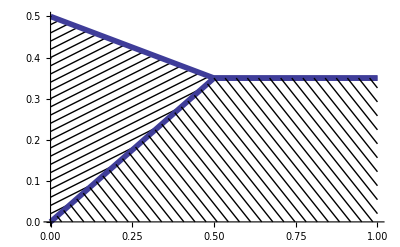

```mathematica
Show[Plot[l4,{x,0,1},PlotStyle->{Black},PlotRange->{{0,1},{0,0.5}}],p4a,p4b,p4smalls]
```

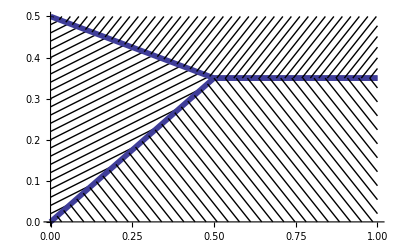

```mathematica
Show[Plot[l4,{x,0,1},PlotStyle->{Black},PlotRange->{{0,1},{0,0.5}}],p4a,p4b,p4smalls,plarges4]
```

```mathematica
ϕc[x_,ψ_]:=If[ψ>su[x],0,If[ψ<sl[x],1,ϕ0]]
```

```mathematica
col[phi_]:=If[phi==0,RGBColor[0,0,0],If[phi==1,RGBColor[255/255,199/255,120/255],If[ϕ0-0.1<=phi<=ϕ0+0.1,RGBColor[189/255,119/255,76/255]]]]
```

```mathematica
ContourPlot[ϕc[x,z],{x,0,1},{z,0,0.5},MaxRecursion->5,ColorFunction->col,AspectRatio->0.5]
```

-Graphics-